```mathematica
d= D[Cos[x],x]
```

```mathematica
-Sin[x]
```

```mathematica
Solve[D[Cos[x],x]==0,x] (* 导数为0处的x点 *)
```

{{x→ConditionalExpression[2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π+2 π C[1],C[1]∈ℤ]}}

```mathematica
D[Sin [2x]/Sin[3x]]
```

Csc[3 x] Sin[2 x]

```mathematica
Plot[{y-x ≤15,x-y≤15},{x,-100,100},PlotLabels->"Expressions"
(*PlotRange->{-8,5},*)(*Ticks->{Range[-2Pi,2Pi,Pi/2],Automatic}*)]
```

-Graphics-

```mathematica
lim= Limit[(2+(1/x))^x,x->Infinity]
```

∞

```mathematica
Plot[Log[E,x],{x,-10,10},PlotLabels->"Expressions",AspectRatio->Automatic,Ticks->{Range[-2Pi,2Pi,Pi/2],Automatic}]
```

-Graphics-

```mathematica
Integrate[x/(√(2x+1)), x]
```

1/3 (-1+x) √(1+2 x)

```mathematica
Plot[1/3 (-1+x) √(1+2 x),{x,-20,20},PlotRange->{-30,30},PlotLabels->"Expressions"]
```

-Graphics-

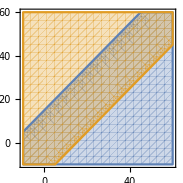

```mathematica
RegionPlot[{y-x≤15,x-y≤15},{x,-10,60},{y,-10,60},AspectRatio->Automatic]
```

```mathematica
RegionPlot[{y-x≤15},{x,-10,60},{y,-10,60},AspectRatio->Automatic]
```

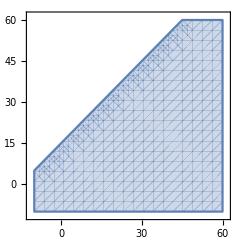

```mathematica
resDist=HypergeometricDistribution[5,6,10] \\
```

```mathematica
N[PDF[resDist,3]]
```

0.47619

下面我们来看看, 这个”超几何分布”模型中, 分别成功(即取到女的) 0次(人), 1次 , 2次, ..., 6次 (因为总共只有6女, 所以最多也只能抽到6女) 的概率, 分别是多少?

```mathematica
listProb = Table[PDF[resDist,i],{i,0,6}]
```

{0,1/42,5/21,10/21,5/21,1/42,0}

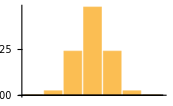

```mathematica
BarChart[listProb]
```